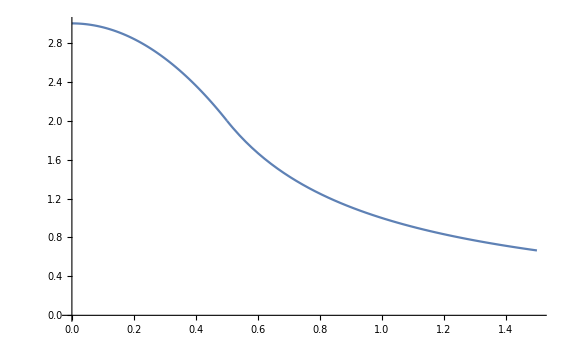

```mathematica
h=1/2;
m=1;
q=1;
p1=Plot[{q/(2h)(3-r^2/h^2)},{r,0,h},PlotRange->{{0,h},{0,(3q)/(2h)}}];

p2=Plot[q/r,{r,h,3h}];
Show[p1,p2,PlotRange->{{0,3h},{0,3 q}}]
```

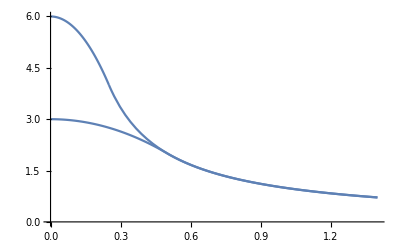

```mathematica
h1=1/2;
p1=Plot[{(m q)/(2 h1)(3-r^2/h1^2)},{r,0,h1},PlotRange->{{0,h1},{0,3/(2h1)}}];

p2=Plot[(m q)/r,{r,h1,1.4}];
h2=1/4;
p3=Plot[{(m q)/(2 h2)(3-r^2/h2^2)},{r,0,h2},PlotRange->{{0, h2},{0,3/(2 h2)}}];

p4=Plot[(m q)/r,{r, h2, 1.4}];
Show[p1,p2,p3,p4,PlotRange->{{0,1.4},{0,3/(2 h2)}},GridLines->{{h1,h2},{6,6}}]
```

```mathematica
F[x_,y_,z_,h_]:=Piecewise[{{q/(2h)(3-(x^2+y^2+z^2)/h^2), x^2+y^2+z^2<h^2}, {q/Sqrt[x^2+y^2+z^2], True}}]
```

```mathematica
Limit[F[x,y,z,h], h->0]
```

Piecewise[{{(m q)/(√(x^2+y^2+z^2)), (x|y|z)∈ℝ&&(x≠0||y≠0||z≠0)}, {Indeterminate, True}}]

```mathematica
h=1; Plot3D[F[x,y,0,h/1],{x,-5h,5h},{y,-5h,5h},PlotRange->All]
```

-Graphics3D-

```mathematica
h=1;ul=Integrate[F[x,y,z,h],{x,-h/2,h/2},{y,-h/2,h/2},{z,-h/2,h/2}]/h^3
```

(11 q)/8

```mathematica
h=1/2;um=Integrate[F[x,y,z,h],{x,-h/2,h/2},{y,-h/2,h/2},{z,-h/2,h/2}]/h^3
```

(11 q)/4

```mathematica
h=1/4;uh=Integrate[F[x,y,z,h],{x,-h/2,h/2},{y,-h/2,h/2},{z,-h/2,h/2}]/h^3
```

(11 q)/2

```mathematica
ul/um
```

1/2

```mathematica
(ul-um)/(um-uh)
```

1/2

```mathematica
Integrate[1/(2hh)(3-r^2/hh^2)4π r^2,{r,0,hh}]/hh^3
```

(8 π)/(5 hh)

```mathematica
ResourceFunction["DarkMode"][]
Z[t_]:={0,xp[t],yp[t],zp[t]}
```

```mathematica
X[t_]:={0,x,y,z}
```

```mathematica
V={ω,xp'[t],yp'[t],zp'[t]};
```

```mathematica
Ψ[x_,y_,z_,h_]:=Piecewise[{{1/(2h)(3-(x^2+y^2+z^2)/h^2), x^2+y^2+z^2<h^2}, {1/Sqrt[x^2+y^2+z^2], True}}]
```

```mathematica
γ[vx_,vy_,vz_]:=1/Sqrt[1-(vx^2+vy^2+vz^2)]
```

```mathematica
B[vx_,vy_,vz_]:=({{γ[vx,vy,vz], -γ[vx,vy,vz]*vx, -γ[vx,vy,vz]*vy, -γ[vx,vy,vz]*vz}, {-γ[vx,vy,vz]*vx, 1+(γ[vx,vy,vz]-1)vx^2/(vx^2+vy^2+vz^2), (γ[vx,vy,vz]-1)(vx*vy)/(vx^2+vy^2+vz^2), (γ[vx,vy,vz]-1)(vx*vz)/(vx^2+vy^2+vz^2)}, {-γ[vx,vy,vz]*vy, (γ[vx,vy,vz]-1)(vx*vy)/(vx^2+vy^2+vz^2), 1+(γ[vx,vy,vz]-1)vy^2/(vx^2+vy^2+vz^2), (γ[vx,vy,vz]-1)(vy*vz)/(vx^2+vy^2+vz^2)}, {-γ[vx,vy,vz]*vz, (γ[vx,vy,vz]-1)(vx*vz)/(vx^2+vy^2+vz^2), (γ[vx,vy,vz]-1)(vy*vz)/(vx^2+vy^2+vz^2), 1+(γ[vx,vy,vz]-1)vz^2/(vx^2+vy^2+vz^2)}})
```

```mathematica
BB=B[V[[2]],V[[3]],V[[4]]];
BP=BB.(X[t]-Z[t]);
```

```mathematica
Φ=Ψ[BP[[2]],BP[[3]],BP[[4]], hh];
Π = D[Φ,t];
```

```mathematica
D[Π,V[[2]]]/.{x->6/10,y->6/10,z->6/10, 
xp[t]->6/10,yp[t]->6/10,zp[t]->6/10,
xp'[t]->1/10,yp'[t]->2/10,zp'[t]->3/10, 
xp''[t]->1/10,yp''[t]->2/10,zp''[t]->3/10, hh->1.0}//N
```

0.

```mathematica
BP/.{x->6/10,y->6/10,z->6/10, 
xp[t]->6/10,yp[t]->6/10,zp[t]->6/10,
xp'[t]->1/10,yp'[t]->2/10,zp'[t]->3/10, 
xp''[t]->1/10,yp''[t]->2/10,zp''[t]->3/10, hh->1.0}//N
```

{0.,0.,0.,0.}